```mathematica
(*Run 1*)
```

0.000100912

0.938272

99/100

249/500

1.7×10^-11

0.00729753

0.1101

0.09207

1.8×10^-7

0.13957

0.000017

0.547855

0.00023

0.775027

0.00013

0.782896

0.000016

1.01946

0.00013

0.00863512

0.0008

0.150074

0.000013

0.00426905

49/50

0.000016

0.493666

0.957759

6.×10^-6

0.000190316

0.957721

-Graphics3D-

0.01

0.701094

0.01

0.631735

0.5

41.7372

0.720486

0.1

0.0572916

-8 °

0.02

0.861776

0.454037

0.398612

0.139943

0.145358

0.203151

-0.213919

0.180985

0.0203418

-0.043458

9.06201

0.00107368

3.16278

35.5825

-2.16613

2.83235

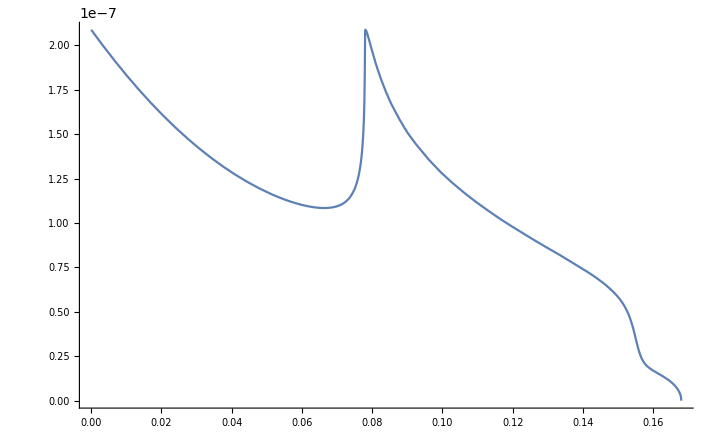

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 20000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000272574 and 7.38587×10^-9 for the integral and error estimates.

0.000272574

1.95455×10^-8

0.0001027

0.000269503

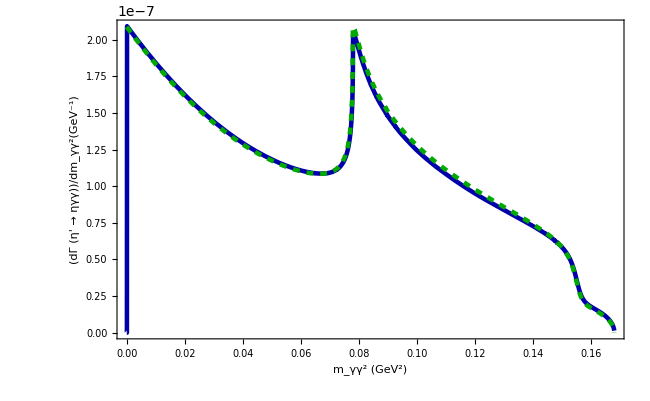

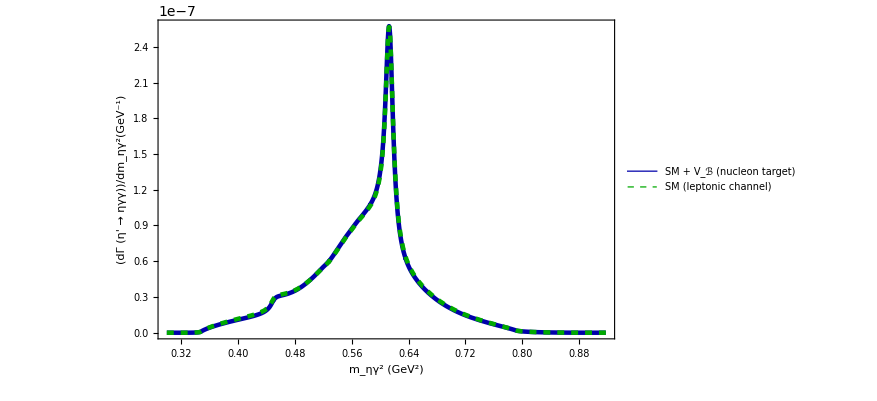

η' → ηγγ: γγ and ηγ Spectra  with and without V_ℬ (Nucleon Target) | 
-Graphics- | -Graphics-

EtaPrimeEtaGammaGamma_1.png

1.9323×10^-8

0.000101531

0.0001027

{1.95455×10^-8,0.0001027}

{1.9323×10^-8,0.000101531}

```mathematica
GenerateValue[M0_,sigma_]:=If[sigma==0,M0,RandomVariate[NormalDistribution[M0,sigma]]]
BestCouplingCoeff = GenerateValue[0.00009474747474747476,5.255114616869139*^-6]
mN=GenerateValue[938.27208816*10^(-3),0.00000029*10^(-3)]
mf0 =990*10^(-3)
mσ=498*10^(-3)
Δα=0.000000017*10^(-3)
α=GenerateValue[7.297525664*10^(-3),Δα]
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
ΔmπA=0.00018*10^(-3)
mπA=GenerateValue[139.57039*10^(-3),ΔmπA]
ΔMη=0.017*10^(-3)
Mη = GenerateValue[547.862*10^(-3),ΔMη]
Δmρ=0.23*10^(-3)
mρ=GenerateValue[775.26*10^(-3),Δmρ]
Δmω=0.13*10^(-3)
mω=GenerateValue[782.66*10^(-3),Δmω]
Δmϕ=0.016*10^(-3)
mϕ=GenerateValue[1019.461*10^(-3),Δmϕ]
ΔΓω =0.13*10^(-3)
Γω = GenerateValue[8.68*10^(-3),ΔΓω]
ΔΓρ=0.8*10^(-3)
Γρ = GenerateValue[149.1*10^(-3),ΔΓρ]
ΔΓϕ=0.013*10^(-3)
Γϕ = GenerateValue[4.249*10^(-3),ΔΓϕ]
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=GenerateValue[493.677*10^(-3),ΔmKP]
MηPrime = GenerateValue[957.78*10^(-3),0.06*10^(-3)]
ΔΓtotal = 0.006*10^(-3)
Γtotal=GenerateValue[0.188*10^(-3),ΔΓtotal]
MηP = GenerateValue[957.78*10^(-3),0.06*10^(-3)]
ΓρEff[t_] :=Γρ*((-4 mπA^2+t)/(-4 mπA^2+mρ^2))^(3/2) *HeavisideTheta[-4 mπA^2+t]
m232MAX[m132_] := ((MηP^2+Mη^2)^2)/(4 m132)-(-(-m132+MηP^2)/(2 √m132)+√(-Mη^2+((m132+Mη^2)^2)/(4 m132)))^2
m232MIN[m132_] := ((MηP^2+Mη^2)^2)/(4 m132)-((-m132+MηP^2)/(2 √m132)+√(-Mη^2+((m132+Mη^2)^2)/(4 m132)))^2
Constraint[m132_, m232_]:=HeavisideTheta[m232MAX[m132]-m232]*HeavisideTheta[m232-m232MIN[m132]]
Plot3D[Constraint[m132, m232], {m132, Mη^2, MηP^2},{m232, Mη^2, MηP^2}, PlotRange->All]
Δg=0.01
g =GenerateValue[0.70,Δg]
ΔzSmBm=0.01
zSmBm =GenerateValue[0.65,ΔzSmBm]
ΔϕP=0.5
GenerateValue[41.4,ΔϕP]
ϕP = (GenerateValue[41.4,ΔϕP])Degree
ΔϕV=0.1
ϕV =(GenerateValue[3.3,ΔϕV])Degree
ϕS = - 8 Degree
ΔzNS=0.02
zNS = GenerateValue[0.83,ΔzNS]
gρηγ = g*zNS*Cos[ϕP]
gρηPγ = g*zNS*Sin[ϕP]
gωηγ =g/3*(zNS*Cos[ϕP]*Cos[ϕV]-2*zSmBm*Sin[ϕP]*Sin[ϕV])
gωηPγ =g/3*(zNS*Sin[ϕP]*Cos[ϕV]+2*zSmBm*Cos[ϕP]*Sin[ϕV])
gϕηγ =g/3*(zNS*Cos[ϕP]*Sin[ϕV]+2*zSmBm*Sin[ϕP]*Cos[ϕV])
gϕηPγ =g/3*(zNS*Sin[ϕP]*Sin[ϕV]-2*zSmBm*Cos[ϕP]*Cos[ϕV])
cρ = gρηγ*gρηPγ
cω = gωηγ*gωηPγ
cϕ = gϕηγ*gϕηPγ
Bq2Bq2p[m132_,m232_]:=1/8 (m132^2+MηP^4) (-m132-m232+MηP^2+Mη^2)^2 +1/8 (-m132+MηP^2) (-m232+MηP^2) (m132 m232+MηP^2 (m132+m232-MηP^2-2 Mη^2))
Bq1Bq1[m132_,m232_]:=1/8 (m232^2+MηP^4) (-m132-m232+MηP^2+Mη^2)^2 +1/8 (-m132+MηP^2) (-m232+MηP^2) (m132 m232+MηP^2 (m132+m232-MηP^2-2 Mη^2))
Bq2Bq1[m132_,m232_]:=1/8 (m132*m232+MηP^4) (-m132-m232+MηP^2+Mη^2)^2 +1/8 (-m132+MηP^2) (-m232+MηP^2) (m132 m232+MηP^2 (m132+m232-MηP^2-2 Mη^2))
BWt[m132_,m232_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)]^2
BWu[m132_,m232_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)]^2
BWtu[m132_,m232_] :=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω))]
βπ[s_]:=√(1-(4 mπA^2)/s)
BARβπ[s_]:=√(-1+(4 mπA^2)/s)
βK[s_]:=√(1-(4 mKP^2)/s)
BARβK[s_]:=√(-1+(4 mKP^2)/s)
θπ[s_]:=HeavisideTheta[-4 mπA^2+s]
BARθπ[s_]:=HeavisideTheta[4 mπA^2-s]
θK[s_]:=HeavisideTheta[-4 mKP^2+s]
BARθK[s_]:=HeavisideTheta[4 mKP^2-s]
gσππSQ=(3 (mπA^2-mσ^2)^2 Cos[ϕS]^2)/(2 fπ^2)
gσKbarKSQ=((mKP^2-mσ^2)^2 (Cos[ϕS]-√2 Sin[ϕS])^2)/(2 fK^2)
Rσ[s_]:=1/(16 π^2)gσKbarKSQ* (2-2 ArcTan[1/BARβK[s]]* BARβK[s]*BARθK[s]-Log[(1+βK[s])/(1-βK[s])] *βK[s] *θK[s])+1/(16 π^2)gσππSQ *(2-2 ArcTan[1/BARβπ[s]] *BARβπ[s]* BARθπ[s]-Log[(1+βπ[s])/(1-βπ[s])] *βπ[s]* θπ[s])
Iσ[s_]:=-(gσKbarKSQ*βK[s]*θK[s])/(16 π)-(gσππSQ*βπ[s]*θπ[s])/(16 π)
Dσ[s_]:=-mσ^2+s+ⅈ Iσ[s]-Rσ[mσ^2]+Rσ[s]
gf0ππSQ=(3 (mπA^2-mf0^2)^2 Sin[ϕS]^2)/(2 fπ^2)
gf0KbarKSQ=((mKP^2-mf0^2)^2 (Sin[ϕS]+√2 Cos[ϕS])^2)/(2 fK^2)
Rf0[s_]:=1/(16 π^2)gf0KbarKSQ *(2-2 ArcTan[1/BARβK[s]]* BARβK[s]*BARθK[s]-Log[(1+βK[s])/(1-βK[s])]* βK[s]*θK[s])+1/(16 π^2)gf0ππSQ (2-2 ArcTan[1/BARβπ[s]]*BARβπ[s]*BARθπ[s]-Log[(1+βπ[s])/(1-βπ[s])]*βπ[s]*θπ[s])
If0[s_]:=-(gf0KbarKSQ*βK[s]*θK[s])/(16 π)-(gf0ππSQ*βπ[s]*θπ[s])/(16 π)
Df0[s_]:=-mf0^2+s+ⅈ Iσ[s]-Rσ[mf0^2]+Rσ[s]
gσηηP=Sin[2 ϕP]/(2 fπ)*((-maZero^2+Mη^2 Cos[ϕP]^2+MηP^2 Sin[ϕP]^2) (Cos[ϕS]+√2 (-1+(2 fK)/fπ) Sin[ϕS])-(-Mη^2+MηP^2) (Cos[2 ϕP] Cos[ϕS]-1/2 Sin[2 ϕP] Sin[ϕS]))
gf0ηηP=Sin[2 ϕP]/(2 fπ)*((-maZero^2+Mη^2 Cos[ϕP]^2+MηP^2 Sin[ϕP]^2) (Sin[ϕS]-√2 (-1+(2 fK)/fπ) Cos[ϕS])-(-Mη^2+MηP^2) (Cos[2 ϕP] Sin[ϕS]+1/2 Sin[2 ϕP] Cos[ϕS]))
AKplusKminusηηP[s_]:=-((1-2 (-1+(2 fK)/fπ)) (-mKP^2+s) Sin[2 ϕP])/(4 fK fπ)+((-mKP^2+s) ((gf0ηηP (√2 Cos[ϕS]+Sin[ϕS]))/Df0[s]+(gσηηP (Cos[ϕS]-√2 Sin[ϕS]))/Dσ[s]))/(2 fK)-1/(4 fπ^2)((-(8 mKP^2)/9+1/3 (-Mη^2-MηP^2)-(2 mπA^2)/9+s) (√2 Cos[2 ϕP]+1/2 Sin[2 ϕP])+4/9 (2 mKP^2-mπA^2) (-Cos[2 ϕP]/(√2)+2 Sin[2 ϕP]))
AπplusπminusηηP[s_]:=((-mπA^2+s)/fπ)*((gf0ηηP*Sin[ϕS])/Df0[s]+(gσηηP*Cos[ϕS])/Dσ[s])+((2 mπA^2-s) Sin[2 ϕS])/(2 fπ^2)
f[z_]:=1/4* HeavisideTheta[1/4-z] *(-ⅈ π+Log[(1+√(1-4 z))/(1-√(1-4 z))])^2-ArcSin[1/(2 √z)]^2 HeavisideTheta[-1/4+z]
L[z_]:=-1/(2 z)-(2 f[1/z])/z^2
Int1VMDLSM[m132_,m232_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+Mη^2+MηP^2)/mKP^2]*AKplusKminusηηP[-m132-m232+Mη^2+MηP^2]+(2 α)/(π*mπA^2)*L[(-m132-m232+Mη^2+MηP^2)/mπA^2]*AπplusπminusηηP[-m132-m232+Mη^2+MηP^2]
Int2VMDLSM[m132_,m232_]:=-Conjugate[1/4 (-m132-m232+Mη^2+MηP^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)))]
Interference[m132_,m232_]:=2*Re[Int1VMDLSM[m132,m232]*Int2VMDLSM[m132,m232]]*Constraint[m132, m232]
LSM[m132_,m232_]:=2/π^2(-m132-m232+Mη^2+MηP^2)^2*Abs[α/mKP^2*L[(-m132-m232+Mη^2+MηP^2)/mKP^2]*AKplusKminusηηP[-m132-m232+Mη^2+MηP^2]+α/mπA^2*L[(-m132-m232+Mη^2+MηP^2)/mπA^2]*AπplusπminusηηP[-m132-m232+Mη^2+MηP^2]]^2*Constraint[m132, m232]

MatrixVMD[m132_,m232_] := (Bq2Bq2p[m132,m232]*BWt[m132,m232]+2*Bq2Bq1[m132,m232]*BWtu[m132,m232] +Bq2Bq1[m132,m232]*BWu[m132,m232])*Constraint[m132, m232]
γγSpectrum[m122_] := NIntegrate[(1/2)*1/(256 MηP^3 π^3)*(MatrixVMD[m132,Mη^2+MηP^2 - m132 - m122]+Interference[m132,Mη^2+MηP^2 - m132 - m122]+LSM[m132,Mη^2+MηP^2 - m132 - m122])*Constraint[m132, Mη^2+MηP^2 - m132 - m122], {m132, Mη^2,MηP^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
pTheory= Plot[γγSpectrum[m122],{m122, 0, (MηP-Mη)^2} , MaxRecursion->5,PlotRange-> All]
IntegrandSM = NIntegrate[MatrixVMD[m132,m232]+Interference[m132,m232]+LSM[m132,m232], {m132, Mη^2, MηP^2}, {m232, Mη^2, MηP^2}, AccuracyGoal->10,Method->{"GlobalAdaptive","MaxErrorIncreases"->20000, Method->"GaussKronrodRule"},MaxRecursion->40]
Width = (1/2)*1/(256 MηP^3 π^3)*(IntegrandSM)
BranchingTheory=Width/Γtotal
BWtDARK[m132_,m232_,Yukawa2Cs2Ms6_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω]^2
BWuDARK[m132_,m232_,Yukawa2Cs2Ms6_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω]^2
BWtuDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)]
MatrixVMDDARK[m132_,m232_,Yukawa2Cs2Ms6_] := (Bq2Bq2p[m132,m232]*BWtDARK[m132,m232,Yukawa2Cs2Ms6]+2*Bq2Bq1[m132,m232]*BWtuDARK[m132,m232,Yukawa2Cs2Ms6] +Bq2Bq1[m132,m232]*BWuDARK[m132,m232,Yukawa2Cs2Ms6])*Constraint[m132, m232]
Int1VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+Mη^2+MηP^2)/mKP^2]*AKplusKminusηηP[-m132-m232+Mη^2+MηP^2]+(2 α)/(π*mπA^2)*L[(-m132-m232+Mη^2+MηP^2)/mπA^2]*AπplusπminusηηP[-m132-m232+Mη^2+MηP^2]
Int2VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=-Conjugate[1/4 (-m132-m232+MηPrime^2+Mη^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω))]
InterferenceDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=2*Re[Int1VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6]*Int2VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6]]*Constraint[m132, m232]
γγSpectrumDARK[m122_,Yukawa2Cs2Ms6_] := NIntegrate[(1/2)*1/(256 MηPrime^3 π^3)*(MatrixVMDDARK[m132,MηPrime^2+Mη^2 - m132 - m122,Yukawa2Cs2Ms6]+InterferenceDARK[m132,MηPrime^2+Mη^2 - m132 - m122,Yukawa2Cs2Ms6]+LSM[m132,MηPrime^2+Mη^2 - m132 - m122])*Constraint[m132, MηPrime^2+Mη^2 - m132 - m122], {m132, Mη^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->50]
IntegrandDark = NIntegrate[MatrixVMDDARK[m132,m232,BestCouplingCoeff]+InterferenceDARK[m132,m232,BestCouplingCoeff]+LSM[m132,m232], {m132, Mη^2, MηPrime^2}, {m232, Mη^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
p1Graph= Plot[{{γγSpectrumDARK[m122,BestCouplingCoeff]},{γγSpectrum[m122]}},{m122, 0, (MηPrime-Mη)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Green], Thickness[0.005], Dashed]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> None, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"SM + V_ℬ (nucleon target)","SM (leptonic channel)"}, LegendFunction->Framed],PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_γγ^2 (GeV^2)","(dΓ (η' →  ηγγ))/dm_γγ^2(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650]
πγIn[m132_] := NIntegrate[MatrixVMD[m132,m232]+Interference[m132,m232]+LSM[m132,m232],  {m232, Mη^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrum[m132_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγIn[m132])
πγDark[m132_,Yukawa2Cs2Ms6_] := NIntegrate[MatrixVMDDARK[m132,m232,Yukawa2Cs2Ms6]+InterferenceDARK[m132,m232,Yukawa2Cs2Ms6]+LSM[m132,m232],  {m232, Mη^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrumDark[m132_,Yukawa2Cs2Ms6_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγDark[m132,Yukawa2Cs2Ms6])
Part2 = Plot[{{πγSpectrumDark[m132,BestCouplingCoeff]},{πγSpectrum[m132]}},{m132, (Mη)^2, (MηPrime)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Green], Thickness[0.005], Dashed],Directive[Darker[Black],Thickness[0.005]],Directive[Darker[Blue],Dotted],Directive[Darker[Pink], Dashed,Thickness[0.005]],Directive[Darker[Red], Thickness[0.005]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"SM + V_ℬ (nucleon target)","SM (leptonic channel)"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_ηγ^2 (GeV^2)","(dΓ (η' →  ηγγ))/dm_ηγ^2(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,Axes->False]
title=Panel[Style["η' → ηγγ: γγ and ηγ Spectra  with and without V_ℬ (Nucleon Target)",White,40],ImageSize->1500,Background->Blue,Alignment->Center];
DependenceVariation=Deploy@Grid[{{title,SpanFromLeft},{p1Graph,Part2}},Dividers->Gray,Spacings->{0,0}]
Export["EtaPrimeEtaGammaGamma_1.png",DependenceVariation,ImageSize->5000]
WidthDark = (1/2)*1/(256 MηPrime^3 π^3)*(IntegrandDark)
BranchingDark=WidthDark/Γtotal
BranchingTheory=Width/Γtotal
SMOutpt={Width,BranchingTheory}
OutputDark={WidthDark,BranchingDark}
```